```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbarc=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbarc)^2; (* MeV^-1 fm^-2*)
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
activeLEC=Select[Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"][[2;;]],#[[3]]!=-1.&];
line=Fit[Transpose[{activeLEC[[All,1]],activeLEC[[All,2]]}],{1,x},x];
fittedLECs=Table[{λ,line/.x->λ,activeLEC[[1,3]]},{λ,Range[activeLEC[[All,1]][[1]],40 activeLEC[[All,1]][[-1]]]}];
(*activeLEC=fittedLECs[[;;;;5]]*)
activeLEC=activeLEC[[;;;;12]]
```

{{8.,-974.194,-1105.1,0.},{20.,-2357.36,-1788.28,4.46},{32.,-3727.18,-1971.84,0.}}

```mathematica
(*one dimer to rule them all*)
eCore=2.2;
ScaleFac=4;
dimerCore=Get["UnivDimerWF"]
dimerCore=Transpose[{dimerCore[[All,1]],ScaleFac dimerCore[[All,2]]}]
```

{{0.170746,0.0685723}}

{{0.170746,0.274289}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x=1/x (e^x-e^-x)/2
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

## ABAB

```mathematica
VlocABAB=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,eta3,w2,w3},
eta2=4 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta2 Exp[-w2 r^2]
]];

WnolocABAB=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,TwoMyOverHBsq},Block[{zeta1,zeta2,a1,c1,a2,c2,ex1,ex2,lamm=lam},
zeta1=-8 Aa^(3/2) (1/TwoMyOverHBsq);
a1=Aa;
c1=Aa;

zeta2=-32 √2 Cc Aa^3 (1/(2 Aa +lamm))^(3/2);

a2=Aa ((2 Aa+3 lam)/(2 Aa+lamm));
c2=Aa;

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];

(-4 Pi r rp) (zeta1 ex1 (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 ex2)
]];
```

## ABAC

```mathematica
VlocABAC=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,w2,eta3,w3,eta4,w4},
eta2=6 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta3=8 Dd (Aa/(lam+2 Aa))^3;
w3= 4 lam Aa/(2 Aa+lam);
eta4=8 Dd Aa^3 (4 Aa^2+6 Aa lam+lam^2)^(-3/2);
w4= 4 lam Aa (Aa+lam)/(4 Aa^2+6 Aa lam+lam^2);
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta4 Exp[-w4 r^2]
]];

WnolocABAC=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,TwoMyOverHBsq},Block[{zeta1,a1,c1,ex1,zeta2,a2,c2,ex2,zeta3,a3,b3,c3,ex3,zeta4,a4,b4,c4,ex4,zeta5,a5,b5,c5,ex5,lamm=lam},
zeta1=-8 Aa^(3/2) (1/TwoMyOverHBsq);
a1=Aa;
c1=Aa;

zeta2=-32 √2 Cc Aa^3 (1/(2 Aa +lamm))^(3/2);
a2=Aa ((2 Aa+3 lam)/(2 Aa+lamm));
c2=Aa;

zeta3=-8 Cc Aa^(3/2);
a3=Aa+lamm;c3=a3;
b3=2 lamm;

zeta4=-8 Dd Aa^3 (Aa+lamm)^(-3/2);
a4=(2 Aa^2+4 Aa lamm+lamm^2)/(2 (Aa+lamm));c4=a4;
b4=lamm^2 (Aa+lamm)^(-1);

zeta5=-16 √2 Dd Aa^3 (2 Aa+lamm)^(-3/2);
a5=(2 Aa^2+5 Aa lamm+lamm^2)/(2 Aa+lamm);
b5=2 lamm;
c5=(Aa+lamm);

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];
ex3=Exp[-a3 r^2-b3 r rp-c3 rp^2];
ex4=Exp[-a4 r^2-b4 r rp-c4 rp^2];
ex5=Exp[-a5 r^2-b5 r rp-c5 rp^2];

(-4 Pi r rp) (zeta1 ex1 (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 ex2+zeta3 ex3+zeta4 ex4+zeta5 ex5)
]];
```

## ABCD

```mathematica
VlocABCD=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,w2,eta3,w3,eta4,w4},
eta2=8 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta3=16 Dd (Aa/(lam+2 Aa))^3;
w3= 4 lam Aa/(2 Aa+lam);
eta4=16 Dd Aa^3 (4 Aa^2+6 Aa lam+lam^2)^(-3/2);
w4= 4 lam Aa (Aa+lam)/(4 Aa^2+6 Aa lam+lam^2);
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta4 Exp[-w4 r^2]
]];
```

## lim_(λ→∞) ABCD

```mathematica
iVlocABCD=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,w2,eta3,w3,eta4,w4},
eta2=8 √2 Cc (Aa/lam)^(3/2);
w2= 2Aa;
eta3=16 Dd (Aa/lam)^3;
w3= 4 Aa;
eta4=16 Dd (Aa/lam)^3;
w4= 4 Aa ;
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta4 Exp[-w4 r^2]
]];
```

```mathematica
dimerCore
```

{{0.170746,0.274289}}

## lim_(λ→∞) ABAB

```mathematica
iVlocABAB=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,eta3,w2,w3},
eta2=4 √2 Cc (Aa/(lam))^(3/2);
w2= 2lam Aa/(lam);
eta2 Exp[-w2 r^2]
]];

iWnolocABAB=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,TwoMyOverHBsq},Block[{zeta1,zeta2,a1,c1,a2,c2,ex1,ex2,lamm=lam},
zeta1=-8 Aa^(3/2) (1/TwoMyOverHBsq);
a1=Aa;
c1=Aa;

zeta2=-32 √2 Cc Aa^3 (1/(lamm))^(3/2);

a2=Aa ((3 lam)/(2 lamm));
c2=Aa;

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];

(-4 Pi r rp) (zeta1 ex1 (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 ex2)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
hDif=N[Rdis/Npoints];
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocABAB[i hDif,lam,c0,d0,a00[[1]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocABAB[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[1]][[2]],TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];
Wmat=(amat+wmat);

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
(*relerr=Norm[Amat.usol-bcol]/Norm[usol];*)
(*Print["relative error in wave-function solution = ",relerr];*)

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
tanDelta
];
```

```mathematica
GetEREP3[l_?NumberQ,rMax_?NumberQ,nPoints_?NumberQ,core_?ArrayQ,LECc_?NumberQ,LECd_?NumberQ,energ_?NumberQ]:=Module[{locall=l},
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-TanDelSwave/Sqrt[mh2 energ ]
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

Using λ=8.fm^-2     C=-974.194MeV  which is renormalized to B(dimer)=2.2MeV

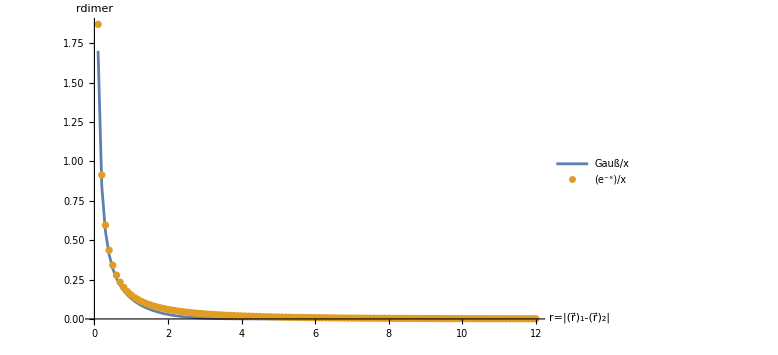

```mathematica
lambdas=activeLEC[[All,1]];
lambdaTest=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Print["Using λ=",Style[lambdaTest,Red],"fm^-2     C=",Style[LECc,Red],"MeV  which is renormalized to B(dimer)=",Style[eCore,Red],"MeV"];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];rR=Range[0.1,12,0.100];
JacobiTrailWavefunctionDataU=Table[R1^-1 JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
plotDataExp=Table[{rr,√((√(Mm eCore))/(2 π hbarc))Exp[-(√(Mm eCore))/hbarc rr] rr^-1},{rr,rR}];
lgd={"Gauß/x","e^-x/x"};

ListPlot[{Transpose[{rR,plotData[[All,2]]}],Transpose[{rR,plotDataExp[[All,2]]}]},AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic,Joined->{True,False},PlotRange->All]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.1;
(* Integration grid *)
rMa=12;
grdPerFermi=13;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

tmp=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,LECd,energ];
AppendTo[results,{lam,LECc,rMa,nGrd,eCore,tmp,tmp/(hbarc/√(Mm Abs[eCore]))}];
Print["λ=",lam," B(2)=",eCore,"  C_0(λ)=",LECc,")  ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbarc/√(Mm Abs[eCore]))];
,{lam,lambdas}];
```

λ=8. B(2)=2.2  C_0(λ)=-974.194)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=2.73218 ; a_dd/a_aa=0.629265

λ=20. B(2)=2.2  C_0(λ)=-2357.36)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=2.92443 ; a_dd/a_aa=0.673544

λ=32. B(2)=2.2  C_0(λ)=-3727.18)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=2.99954 ; a_dd/a_aa=0.690843

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

```mathematica
grdPerFermi=14;
rMi=0.0001;
rMa=24;
nGrd=IntegerPart[rMa grdPerFermi];
Grd=Range[0,rMa,1/grdPerFermi][[2;;]];

results={};
resultsWF={};
runtimes={};

alpha0=10;
m0=0.7;
exp0=2.5;
(*SetSharedVariable[results,resultsPhases];*)
Do[
dimerCore[[1]][[2]]=alpha0 ArcTan[m0 lam]^(exp0);
(*dimerCore={{1,alpha0-exp0/(1+Exp[-m0 lam])}};*)
(*dimerCore={{1,alpha0 Log[(m0 lam)]^(exp0)}};*)
(*dimerCore={{1,alpha0 Exp[-m0 lam]+exp0}};*)
(*dimerCore={{1,alpha0+(lam exp0)/(lam+m0)}};*)
LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];
tmp=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,LECd,energ];
AppendTo[results,tmp];
(*Print["λ = ",lam,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbarc/√(Mm Abs[eCore])),Red,18]];*)
,{lam,lambdas}]
```

1.1

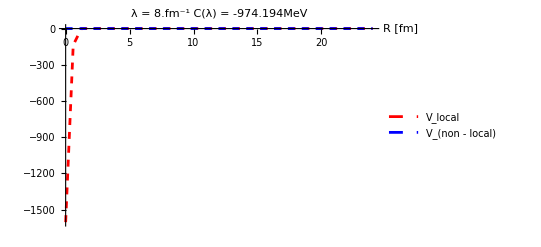

-Graphics3D-

```mathematica
rP=1.1
lam=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

Plot[
{VlocABAB[R,lam,LECc,LECd,dimerCore[[1]][[2]]],Re[WnolocABAB[R,rP,energ,lam,LECc,LECd,dimerCore[[1]][[2]],mh2]]},{R,rMi,rMa},PlotPoints->40,MaxRecursion->0,PlotLegends->{"V_local","V_(non - local)"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},AxesLabel->{"R [fm]"},PlotLabel->"λ = "<>ToString[lam]<>"fm^-1    C(λ) = "<>ToString[LECc]<>"MeV",PlotRange->Full]

Plot3D[Re[WnolocABAB[rr,rp,energ,lam,LECc,LECd,dimerCore[[1]][[2]],mh2]],{rr,rMi,rMa},{rp,0.01,rMa},PlotRange->Full]
```

```mathematica
aDDofLam[a_?NumberQ,b_?NumberQ,e_?NumberQ]:=Block[{target=2.1,resuls={},rM=16,nG=12},
Do[
wfWidth=a ArcTan[b lam]^e;

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

momFM=Sqrt[mh2 energ];

hDif=N[rM/nG];
energyMeV=(momFM^2)/mh2;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nG,nG}];

amat=DiagonalMatrix[Table[-hDif^2 mh2 VlocABAB[i hDif,lam,LECc,LECd,wfWidth],{i,1,nG}]];

wmat=Table[-hDif^3 mh2 WnolocABAB[i hDif,j hDif,energyMeV,lam,LECc,LECd,wfWidth,mh2],{i,1,nG},{j,1,nG}];
Wmat=(amat+wmat);

Dmat=DiagonalMatrix[Table[hDif^2 (momFM^2),{i,1,nG}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,nG];
ucol=Array[Subscript["u", ##]&,{nG}];

bcol⟦-1⟧=- beta[rM,momFM,0,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[rM,momFM,0,hDif];

usol=LinearSolve[Amat,bcol];
(*relerr=Norm[Amat.usol-bcol]/Norm[usol];*)
(*Print["relative error in wave-function solution = ",relerr];*)

tanDelta= (RiccatiBesselJ[momFM rM,0]/RiccatiBesselN[momFM rM,0])-(usol⟦-1⟧/RiccatiBesselN[momFM rM,0]);
(*sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momFM rM,0]-RiccatiBesselN[momFM rM,0] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];*)

(*TanDelSwave=SolveSecularP3[rMa,nGrd,momFM,0,lam,LECc,LECd,dimerCore,mh2];*)
add=-tanDelta/Sqrt[mh2 energyMeV ];

AppendTo[resuls,add];

,{lam,lambdas}];

xhisq=Table[(resuls[[nn]]-target)^2,{nn,Range[Length[lambdas]]}];
Total[xhisq]
]
```

```mathematica
solKLM=NMinimize[{aDDofLam[k,l,m],l>=0,k>=0},{k∈Reals,l∈Reals,m∈Reals},Method->"RandomSearch",AccuracyGoal->6,PrecisionGoal->5]
```

{3.58817×10^-16,{k→0.488044,l→0.0686167,m→0.151664}}

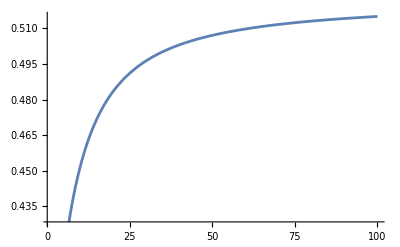

```mathematica
Plot[(k ArcTan[l λ]^m)/.solKLM[[2]],{λ,1,100}]
```